```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

## Seek spirals between the fixed point #1 and points of height n on the critical line.

```mathematica
stream=OpenRead["zeta1fixedpts13dec15"];
ls=ReadList[stream];
Close[stream];
stream1=OpenWrite["run 1->ni24jan16no6"];
stream2=OpenWrite["nonlinearmodels24jan16no6"];
fx=ls[[1,2]];
Print["fixed point"];
Print[fx];
For[n=10,n<100,n=n+1/10;
precision=100;
polardata={};
polardata2={};

zr=1/2+n*I;
terminator=zr;
zeros={zr};
la=Re[Log[Abs[zr-fx]]];
arg=Arg[zr-fx];
args={arg};
polardata=Append[polardata,{la*Cos[arg],la*Sin[arg]}];
polardata2=Append[polardata2,{arg,la}];
Write[stream1,{n,1,zr,arg,la}];


For[k=1,k<60,k++;
startcenter=fx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision,WorkingPrecision->precision][[1,2]];
zeros=Append[zeros,zr];
la=Re[Log[Abs[zr-fx]]];
arg=Arg[zr-fx];
While[Not[arg>Last[args]],arg=arg+2*Pi];
args=Append[args,arg];
polardata=Append[polardata,{la*Cos[arg],la*Sin[arg]}];
polardata2=Append[polardata2,{arg,la}];
Write[stream1,{n,k,zr,arg,la}]];
(*end k loop *)

nlm=NonlinearModelFit[polardata2,a Exp[c u]+b+d u,{a,b,c,d},u];
Write[stream2,Flatten[{n,nlm[[1,2]]}]]
];

Close[stream1];
Close[stream2]
```

fixed point

-2.3859356834242454303981832757445930362201093149638873351574932048323476335235960582494742538336295338847805249615938408447474759057948504653854416873443752760902584244284522229881886715785738874413702535122548414406542818655672055585034584201209569528634191891134381295468833452400850690260662752914559195280705613430001186829694135706608379968929630898290058414119570561055870643268241892297797977153584811066572063496935973867132888293939060626696523874543041024973635338257262787980180919648850104+16.270987062196790172331511742426448038886999328508061422303987474531246081745277351151466976628577373976216826920280848966368860320907877000338327930829150746067040105143465540304695275115154253306241209986363610897068261341486909527958514699198902797101508934743244353586768639349093984061186540474043223172673718916752005164408050492742771411730858141343093378534405204100963939479247183911745169149366416883274923778990528518777554930804685204679129738412465846884027858770239057857955670276162524 ⅈ

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

nonlinearmodels24jan16no6

```mathematica
stream=OpenRead["nonlinearmodels24jan16no6"];
models=ReadList[stream];
Close[stream];
```

```mathematica
models[[1]]
```

{101/10,6.746589723528887647865623157048×10^-14→-4.12738744976503830380644039669×10^-14,7.214117926583169792196272010909→-0.338953256429115800445572918251,0.3956719115765182816063762040441→0.407436292434543669775396473327,-2.396698464036307313100715134776→-2.39396929402654828873974178821}

```mathematica
stream=OpenRead["nonlinearmodels24jan16no6"];
models=ReadList[stream];
Close[stream];
adata={};
bdata={};
cdata={};
ddata={};
For[n=0,n<Length[models],
n++;
a=models[[n,2,2]];
b=models[[n,3,2]];
c=models[[n,4,2]];
d=models[[n,5,2]];
adata=Append[adata,{models[[n,1]],Re[Log[Abs[a]]]}];
bdata=Append[bdata,{models[[n,1]],b}];
cdata=Append[cdata,{models[[n,1]],c}];
ddata=Append[ddata,{models[[n,1]],d}]];
Print["a data"];
Print[ListPlot[adata]];
Print["b data"];
Print[ListPlot[bdata]];
Print["c data"];
Print[ListPlot[cdata]];
Print["d data"];
Print[ListPlot[ddata]]
```

a data

## fig 15c

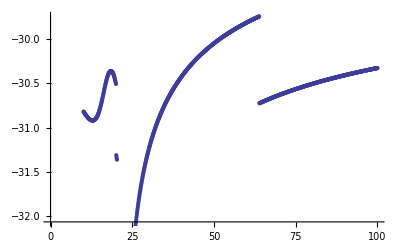

b data

## fig 15a

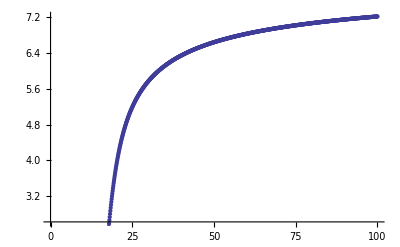

c data

## fig 15d

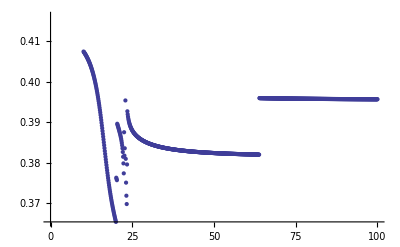

d data

## fig 15b

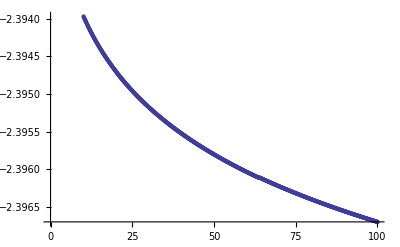

```mathematica
stream=OpenRead["run 1->ni24jan16no6"];
list=ReadList[stream];
Close[stream]
```

run 1->ni24jan16no6

```mathematica
Length[list]
```

54000

n  12

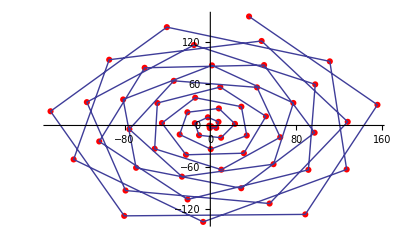

n  13

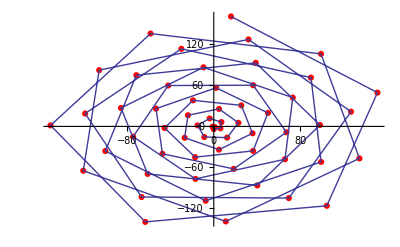

n  14

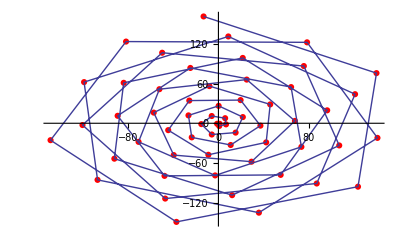

n  15

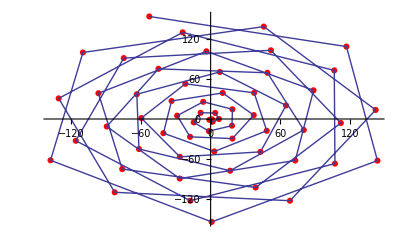

n  16

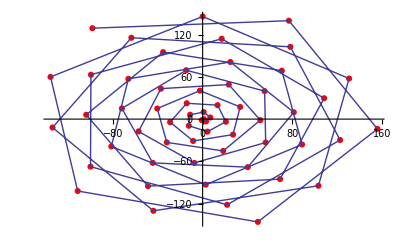

```mathematica
For[n=11,n<16,n++;
pairs={};
For[j=0,j<Length[list],j++;
If[n==list[[j,1]],
arg=list[[j,4]];
la=list[[j,5]];
pair={la*Cos[arg],la*Sin[arg]};
pairs=Append[pairs,pair]
] (*  close  If *)
];(* close j *)
Print["n  ",n];
redplot=ListPlot[pairs,PlotStyle->{Red,PointSize[.011]}];
jplot=ListPlot[pairs,Joined->True];
Print[Show[redplot,jplot]]
] (* close n *)
```

n  12

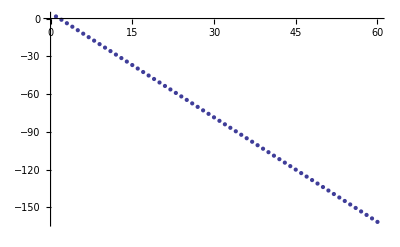

n  13

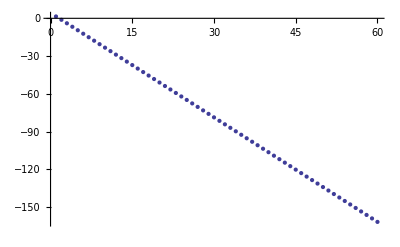

n  14

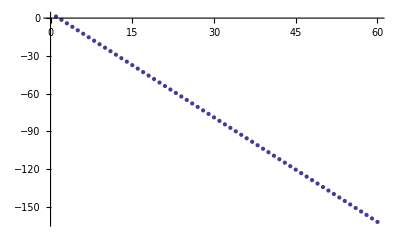

n  15

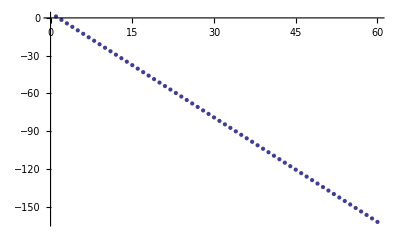

n  16

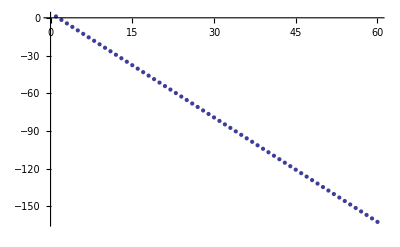

```mathematica
For[n=11,n<16,n++;
pairs={};
For[j=0,j<Length[list],j++;
If[n==list[[j,1]],
k=list[[j,2]];
la=list[[j,5]];
pair={k,la};
pairs=Append[pairs,pair]
] (*  close  If *)
];(* close j *)
Print["n  ",n];
Print[ListPlot[pairs]]
] (* close n *)
```